```mathematica
Needs["Constants`",NotebookDirectory[]<>"../packages/Constants.wl"]
Needs["Capture`",NotebookDirectory[]<>"../packages/Capture.wl"]
Needs["Utilities`",NotebookDirectory[]<>"../packages/Utilities.wl"]
Needs["Dielectrics`",NotebookDirectory[]<>"../packages/Dielectrics.wl"]
Needs["FormFactors`",NotebookDirectory[]<>"../packages/FormFactors.wl"]
Needs["EnergyLoss`",NotebookDirectory[]<>"../packages/EnergyLoss.wl"]
```

dσdΩNuc0::shdw: Symbol dσdΩNuc0 appears in multiple contexts {Capture`,Global`}; definitions in context Capture` may shadow or be shadowed by other definitions.

GetNMaxofdσdΩNuc0::shdw: Symbol GetNMaxofdσdΩNuc0 appears in multiple contexts {Capture`,Global`}; definitions in context Capture` may shadow or be shadowed by other definitions.

GetωandcosθNuc0::shdw: Symbol GetωandcosθNuc0 appears in multiple contexts {Capture`,Global`}; definitions in context Capture` may shadow or be shadowed by other definitions.

InterpolatedσdERdσMax::shdw: Symbol InterpolatedσdERdσMax appears in multiple contexts {Capture`,Global`}; definitions in context Capture` may shadow or be shadowed by other definitions.

```mathematica
testmodule[]:=Module[{mχ},
mχ="mχ" /.{<|"mχ"->3|>,<|"mχ"->3|>,<|"mχ"->3|>,<|"mχ"->3|>};
If[Length@Union[mχ]==1,mχ[[1]],Print["mχ must be the same in all processes"];Return[<||>,Module]]
]
```

```mathematica
testmodule[]
```

3

### Nuclear Scattering

```mathematica
dσdΩNuc0[cosθ_,vχ_,κ_,mχ_,coeffs_,params_]:=Module[{mN,ω,qpm,ξθ,Sofqω,dσdΩ},
(* Get dσ/(dΩ) for nuclear scattering at 0 temperature. At 0 temperature there is a delta function which gives ω in terms of q (and hence cosθ through q_0)
  cosθ ϵ (0,1) - [] negative disallowed since gas is assumed 0 T: hence no energy can be removed from the nuclei.*)
mN ="mN"/. coeffs;
ω=(2 cosθ^2 mN mχ^2 vχ^2)/((mN+mχ)^2 "ℏ")/.params; (*define ω in terms of cosθ*)
qpm={q->(mχ vχ)/("ℏ") (cosθ-Sqrt[cosθ^2-(2ω "ℏ")/(mχ vχ^2)]),q->(mχ vχ)/("ℏ") (cosθ+Sqrt[cosθ^2-(2ω "ℏ")/(mχ vχ^2)])}/.params;(*solutions for q to ω-ω(q,cosθ)=0 in the delta function that arises in the q integral. These must be summed over*)
ξθ=Sqrt[cosθ^2-(2 "ℏ" ω)/(mχ vχ^2)]/.params;(*the absolute value of the jacobian of the delta function, evaluated on the roots of q in the argument, for each of the above solutions*)

dσdΩ =Total@Table[1/(vχ^2 )  q^2/(("ℏ")^2 (2 π)^3) 1/ξθ ((κ ("e")^2)/(4 π "ϵ0" q^2))^2 FormFactors`Zeff[q,coeffs]/.qpm[[i]]/.params,{i,2}];

<|"dσdΩ"->dσdΩ,"ω"->ω,"cosθ"->cosθ,"ξpm"->ξθ,"qpm"->qpm|>
]
```

```mathematica
GetNMaxofdσdΩNuc0[vχ_,mχ_,coeffs_,params_,buffer_:1.1 ,δ_:10^-3]:=Module[{},
(*vχmax=10^-3 "c"/.Constants`SIConstRepl;*)
buffer NMaximize[Total@dσdΩNuc0[cosθ,vχ,1,mχ,coeffs,params][["dσdΩ"]],cosθ∈Interval[{δ,1-δ}]][[1]]
]
```

```mathematica
GetωandcosθNuc0[vχ_,mχ_,coeffs_,params_,NMax_]:=Module[{nits=0,cosθ,Mξ,dσdΩ,ω,Accepted=False,Errors=0},
While[!Accepted,
nits+=1;
cosθ=Random[];(*assumes 0 temp so cosθ > 0*)
Mξ=NMax Random[];
(*σs=Total[dσdERdΩeofvχandϵ[ξs[[1]],ξs[[2]],vχ,1,ϵDict][["dσdERdΩ"]]];*)
{dσdΩ,ω}={"dσdΩ","ω"}/.dσdΩNuc0[cosθ,vχ,1,mχ,coeffs,params];(*Set κ to 1, overall scaling is irrelevant*)
(*dσdΩ=Total[dσdΩ];*)
Accepted=Mξ<= dσdΩ;
Errors=If[dσdΩ-NMax> 0,Break[];True,0];
];
<|"ω"->ω,"cosθ"->cosθ,"Mξ"->Mξ,"dσdERdΩ"->dσdΩ,"Max"->NMax,"Errors"->Errors,"nits"->nits|>
]
```

```mathematica
InterpolatedσdERdσMax[dσdERdΩMaxf_,m_:20,uselog_:True]:=Module[{vχMax,vχMin,vχs,MaxInterTable,MaxInterf},
vχMax = 2 10^-1 "c" /.Constants`SIConstRepl;
vχMin = 1/10 Constants`vescape;
vχs = N@If[uselog,10^Subdivide[Log10[vχMin],Log10[vχMax],m],Subdivide[vχMin,vχMax,m]];
MaxInterTable = Table[{vχs[[i]],dσdERdΩMaxf[vχs[[i]]]},{i,m}];
MaxInterf=If[uselog,Interpolation[Log10[MaxInterTable],InterpolationOrder->4],Interpolation[MaxInterTable,InterpolationOrder->4]];
<|"Maxf"->MaxInterf,"MaxTable"->MaxInterTable,"vχs"->vχs,"vχrange"->{vχMin,vχMax}|>
]
```

```mathematica
ProcessDataAssemblerNuclear[mχ_,coeffs_,params_,dσdERdΩsampler_,λDict_,RegionNum_:1,Save_:False,fname_:"procdata",ProcNum_:1,uselog_:True,m_:200,n_:200,δ_:10^-7]:= Module[{dσdERdΩMaxloglog,dσdERdΩMax,dσdERdΩsample,σ,outdict},
dσdERdΩMaxloglog = "Maxf"/.InterpolatedσdERdσMax[GetNMaxofdσdΩNuc0[#,mχ,coeffs,params]&];
dσdERdΩMax=(10^dσdERdΩMaxloglog[Log10[#]])&;
dσdERdΩsample = GetωandcosθNuc0[#,mχ,coeffs,params,dσdERdΩMax[#]]&;

σ=1/("ne"/.λDict["fitparams"][[1]]) 10^("f"/.λDict)[Log10[mχ],Log10[#]]&;
outdict=<|"ProcNum"->ProcNum,"dσdERdΩMax"->dσdERdΩMax,"dσdERdΩsample"->dσdERdΩsample,"σ"->σ,"λ"->λDict["f"],"region"->RegionNum,"mχ"->mχ|>;
If[Save,Utilities`SaveIt[NotebookDirectory[]<>fname,outdict]];(*Note that we have to save the object internally in the package to use it in the package. It is saved as private so can only be accessed from in here.*)
outdict 
]
```

We get σ and λ from the dσdER interpolations we did.

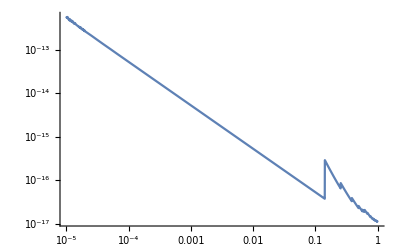

```mathematica
LogLogPlot[dσdΩNuc0[cosθ,10^4,1,"m"/.SIConstRepl,FeNucCoeffs,SIConstRepl][["dσdΩ"]],{cosθ,10^-5,1}]
```

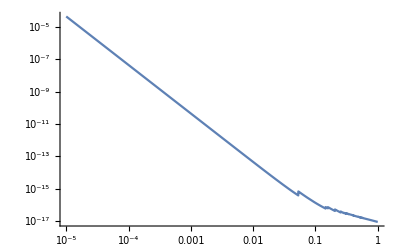

```mathematica
LogLogPlot[dσdΩNuc0[cosθ,10^4,1,"m"/.SIConstRepl,SiNucCoeffs,SIConstRepl][["dσdΩ"]],{cosθ,10^-5,1}]
```

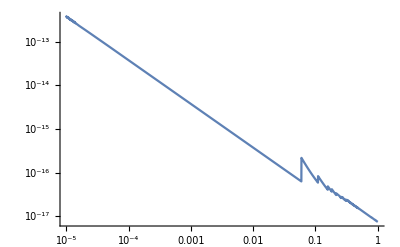

```mathematica
LogLogPlot[dσdΩNuc0[cosθ,10^4,1,"m"/.SIConstRepl,MgNucCoeffs,SIConstRepl][["dσdΩ"]],{cosθ,10^-5,1}]
```

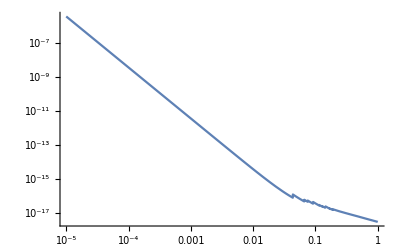

```mathematica
LogLogPlot[dσdΩNuc0[cosθ,10^4,1,"m"/.SIConstRepl,ONucCoeffs,SIConstRepl][["dσdΩ"]],{cosθ,10^-5,1}]
```

Do the interpolation internally

```mathematica
InterpolatevχandωσdERNucξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-7,2 10^-1}"c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,20,60,10^-4];
```

General::munfl: Exp[-790.662] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-921.843] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1074.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(#2^2)&[70,6]
```

36

#### Single Oscillator

```mathematica
testMCprivaterun[FeTotalparams[[2]],FeλeDictOscillators[[2]],NotebookDirectory[]<>"ProcDataTest"]
```

```mathematica
FeOsc2test=ProcessDataAssemblerElectronic[10 "m"/.Constants`SIConstRepl,FeTotalparams[[2]],Getξωandcosθ,FeλeDictOscillators[[2]],2]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

InterpolatingFunction::dmval: Input value {-1.18931,1.17302} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.44118,1.18266} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.876823,1.17215} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

```mathematica
{"λ"/.FeOsc2test};
Getl[10"m"/.Constants`SIConstRepl,10^5,10^-6.5,%]
{"σ"/.FeOsc2test};
σselector[Table[%[[i]][10^5],{i,Length[%]}]]
{"dσdERdΩMax"/.FeOsc2test}[[1]][10^5]
{"dσdERdΩsample"/.FeOsc2test}[[1]][10^5]
```

19009.3

1

0.0355309

<|ξω→0.80182,ω→1.09501×10^14,cosθ→0.562409,Mξ→0.000730204,dσdERdΩ→0.00135325,Max→0.0355309,Errors→0,nits→13|>

```mathematica
?RunMC
```

```mathematica
RunMC[10 "m"/.Constants`SIConstRepl,10^-6.5,("vχ"/.GetvχatEarth[ 10"m"/.Constants`SIConstRepl,(0.001"JpereV"/.Constants`SIConstRepl)^-1]),{"λ"/.FeOsc2test},{"σ"/.FeOsc2test},{"dσdERdΩsample"/.FeOsc2test}]
```

{-11156.4,-753.928,-727.752}

6.371×10^6

InterpolatingFunction::dmval: Input value {-29.0405,4.04943} lies outside the range of data in the interpolating function. Extrapolation will be used.

Process number: 1

InterpolatingFunction::dmval: Input value {-29.0405,4.04943} lies outside the range of data in the interpolating function. Extrapolation will be used.

l is 8252.37

vχ is {-15799.7,-753.928,-727.752}

|vχ| is 15834.4

r is 6.36278×10^6

True

6.24959×10^-25

0.0263678

{-15804.7,-387.896,-784.297}

<|ER→6.24959×10^-25,vχ→{-15804.7,-387.896,-784.297},|vχ|→15828.9,ϕ→1.7233,l→8252.37,cosθ→0.0263678,q→3.19851×10^7,r→6.36278×10^6,reached?→True,κ→3.16228×10^-7,nits→0,ncaptured→0,nescaped→0|>

#### Multiple Oscillators, Just Iron

```mathematica
FeDatae=Table[ProcessDataAssemblerElectronic[10 "m"/.SIConstRepl,FeTotalparams[[i]],Getξωandcosθ,FeλeDictOscillators[[i]],i],{i,Length[FeTotalparams]}]
```

NMaximize::nnum: The function value (0.+2.04313×10^11 ⅈ) 10^(«1»)+(0.+2.04313×10^11 ⅈ) 10^(«1») is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::nnum: The function value (0.+2.52824×10^11 ⅈ) 10^(«1»)+(0.+2.52824×10^11 ⅈ) 10^(«1») is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

InterpolatingFunction::dmval: Input value {-1.10062,1.2617} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-1.3525,1.27134} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.788141,1.26083} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMaximize::cvmit will be suppressed during this calculation.

NMaximize::nnum: The function value (0.+1.13072×10^11 ⅈ) 10^(«1»)+(0.+1.13072×10^11 ⅈ) 10^(«1»[-5.3899+0.10859 ⅈ,-4.3899-0.10859 ⅈ]) is not a number at {cosθ,ξω} = {0.0191284,0.876688}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

```mathematica
SaveIt[NotebookDirectory[]<>"FeDataeTest",FeDatae]
```

C:\Users\keega\OneDrive\Documents\THEP\aDM Capture\notebooks\AdM_capture\aDM_git\capture\FeDataeTest.dat

```mathematica
RunMC[10 "m"/.Constants`SIConstRepl,10^-7.5,("vχ"/.GetvχatEarth[ 10"m"/.Constants`SIConstRepl,(0.001"JpereV"/.Constants`SIConstRepl)^-1]),"λ"/.FeDatae,"σ"/.FeDatae,"dσdERdΩsample"/.FeDatae]
```

{-10647.8,60.5512,253.538}

6.371×10^6

InterpolatingFunction::dmval: Input value {-29.0405,4.02739} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

<|ER→9.01966×10^-26,vχ→{-39159.9,-11743.2,-5533.78},|vχ|→41255.5,ϕ→6.18107,l→1.47896×10^7,cosθ→0.00359785,q→1.21511×10^7,r→1.29209×10^7,reached?→True,κ→3.16228×10^-8,nits→13,ncaptured→0,nescaped→1|>

```mathematica
Re[1 + I]
```

1

#### Iterate mc for iron

```mathematica
IteratreRunMC[1]
```

InterpolatingFunction::dmval: Input value {-29.0405,4.12029} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

l is 1.94115×10^6

vχ is {-18152.3,-1284.05,-140.041}

|vχ| is 18198.2

r is 4.43918×10^6

True

particle is in the crust

Process number: 3

vχ after scatter is {-18120.7,-848.968,-450.52}

l is 88633.5

vχ is {-22061.7,-848.968,-450.52}

|vχ| is 22082.6

r is 4.35067×10^6

True

particle is in the crust

Process number: 7

vχ after scatter is {-22065.7,-686.991,-475.741}

l is 223190.

vχ is {-25459.1,-686.991,-475.741}

|vχ| is 25472.8

r is 4.12764×10^6

True

particle is in the crust

Process number: 7

vχ after scatter is {-21310.7,7566.08,-4048.24}

l is 2.78074×10^6

vχ is {-25257.9,7566.08,-4048.24}

|vχ| is 26675.7

r is 1.54816×10^6

True

particle is in the core

Process number: 1

vχ after scatter is {-21272.1,10872.6,-7381.09}

l is 3.64225×10^6

vχ is {-25225.1,10872.6,-7381.09}

|vχ| is 28442.9

r is 1.55049×10^6

True

particle is in the core

Process number: 3

vχ after scatter is {-25390.2,10317.6,-7579.11}

l is 6.11563×10^6

vχ is {-28436.3,10317.6,-7579.11}

|vχ| is 31185.2

r is 3.91025×10^6

True

particle is in the crust

Process number: 7

vχ after scatter is {-28449.5,10279.1,-7581.89}

l is 3.7024×10^6

vχ is {-31566.4,10279.1,-7581.89}

|vχ| is 34052.7

r is 532642.

True

particle is in the core

Process number: 1

vχ after scatter is {-32062.5,8709.55,-7252.45}

l is 1.69611×10^6

vχ is {-34839.,8709.55,-7252.45}

|vχ| is 36636.2

r is 1.06649×10^6

True

particle is in the core

Process number: 1

vχ after scatter is {-34984.1,8528.92,-6686.77}

l is 2.3551×10^6

vχ is {-37539.8,8528.92,-6686.77}

|vχ| is 39072.9

r is 1.18314×10^6

True

particle is in the core

Process number: 1

vχ after scatter is {-37605.9,6551.36,-7985.4}

l is 2.73733×10^6

vχ is {-39980.5,6551.36,-7985.4}

|vχ| is 41293.2

r is 1.45644×10^6

True

particle is in the core

Process number: 1

vχ after scatter is {-39949.7,6985.94,-7751.56}

l is 4.82061×10^6

vχ is {-42043.3,6985.94,-7751.56}

|vχ| is 43318.9

r is 3.20768×10^6

True

particle is in the core

Process number: 3

vχ after scatter is {-42038.5,7004.35,-7760.72}

l is 7.58316×10^6

vχ is {-43911.4,7004.35,-7760.72}

|vχ| is 45138.6

r is 4.15135×10^6

True

particle is in the crust

Process number: 1

vχ after scatter is {-43194.6,2170.39,-10805.2}

l is 9.92521×10^6

vχ is {-44802.6,2170.39,-10805.2}

|vχ| is 46138.3

r is 5.46576×10^6

True

particle is in the crust

Process number: 7

vχ after scatter is {-44866.2,4860.55,-3010.89}

l is 816346.

vχ is {-46552.1,4860.55,-3010.89}

|vχ| is 46901.9

r is 4.65596×10^6

True

particle is in the crust

Process number: 1

vχ after scatter is {-46396.8,5795.76,-3481.88}

l is 1.05881×10^6

vχ is {-48167.6,5795.76,-3481.88}

|vχ| is 48639.8

r is 3.60821×10^6

True

particle is in the crust

Process number: 7

vχ after scatter is {-42820.2,3974.25,12275.3}

l is 346307.

vχ is {-44772.1,3974.25,12275.3}

|vχ| is 46594.2

r is 3.27663×10^6

True

particle is in the core

Process number: 3

vχ after scatter is {-44784.1,3924.87,12244.6}

l is 5.76204×10^6

vχ is {-46746.6,3924.87,12244.6}

|vχ| is 48482.8

r is 2.26165×10^6

True

particle is in the core

Process number: 1

vχ after scatter is {-43339.4,9082.11,17499.7}

l is 3.79452×10^6

vχ is {-45427.,9082.11,17499.7}

|vχ| is 49521.1

r is 1.19226×10^6

True

particle is in the core

Process number: 1

vχ after scatter is {-45574.9,9365.9,16929.8}

l is 6.63646×10^6

vχ is {-47194.9,9365.9,16929.8}

|vχ| is 51006.8

r is 4.91652×10^6

True

particle is in the crust

Process number: 7

vχ after scatter is {-40792.2,3026.51,27119.1}

l is 553645.

vχ is {-42672.3,3026.51,27119.1}

|vχ| is 50651.1

r is 4.45634×10^6

True

particle is in the crust

Process number: 7

vχ after scatter is {-42356.4,2556.91,27643.4}

l is 42732.7

vχ is {-44175.5,2556.91,27643.4}

|vχ| is 52174.4

r is 4.4206×10^6

True

particle is in the crust

Process number: 1

vχ after scatter is {-45408.5,7389.01,23749.5}

l is 2.55878×10^6

vχ is {-47351.3,7389.01,23749.5}

|vχ| is 53486.3

r is 2.17643×10^6

True

particle is in the core

Process number: 1

vχ after scatter is {-47484.5,7477.69,23449.5}

l is 2.32013×10^6

vχ is {-49419.3,7477.69,23449.5}

|vχ| is 55209.3

r is 116565.

True

particle is in the core

Process number: 1

vχ after scatter is {-48065.,11943.3,23876.7}

l is 198592.

vχ is {-49977.5,11943.3,23876.7}

|vχ| is 56661.2

r is 57044.7

True

particle is in the core

Process number: 1

vχ after scatter is {-49961.7,11986.5,23888.}

l is 8.67712×10^6

vχ is {-51000.4,11986.5,23888.}

|vχ| is 57579.1

r is 7.59412×10^6

True

particle is in space

<|ER→1.02073×10^-26,vχ→{-51000.4,11986.5,23888.},|vχ|→57579.1,ϕ→1.2051,l→8.67712×10^6,cosθ→0.000922313,q→4.08767×10^6,r→7.59412×10^6,reached?→True,κ→1.×10^-8,nits→25,ncaptured→0,nescaped→1|>

ncaptured 0

nescaped 1

nended 0

```mathematica
SortProcessesByRegion[FeDatae,"σ"]
```

{{},{10^((f/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{1525.02,371820.,546795.,4.73051×10^6},{7.96566×10^6,9.21494×10^6,6.93452×10^7,7.86274×10^6},{1.73809×10^8,2.74905×10^8,3.62335×10^8,7.91568×10^6},{2.48614×10^9,1.37255×10^9,3.71001×10^8,7.78732×10^6},{3.88274×10^9,1.48476×10^9,3.71582×10^8,7.8643×10^6},{3.96762×10^9,1.48985×10^9,3.71401×10^8,7.91496×10^6},{3.96793×10^9,1.49321×10^9,3.62938×10^8,8.33211×10^6},{3.9546×10^9,1.49243×10^9,3.71338×10^8,7.91438×10^6}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14}},fname→FeλeDictSIOscillator_1,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{678.612,331.39,149.021,99.7351},{317.447,140.308,83.7021,100.235},{186.721,0.265061,77.1013,74.7758},{0.87419,71.2863,54.303,126.181},{69.8377,90.6639,280.205,339.714},{68.9292,149.287,228.687,166.041},{161.396,166.443,261.367,171.726},{143.639,83.1087,89.1239,75.6897}},totalTime→5037.82|>)[Log10[9.11×10^-30],Log10[#1]])/(ne/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{1525.02,371820.,546795.,4.73051×10^6},{7.96566×10^6,9.21494×10^6,6.93452×10^7,7.86274×10^6},{1.73809×10^8,2.74905×10^8,3.62335×10^8,7.91568×10^6},{2.48614×10^9,1.37255×10^9,3.71001×10^8,7.78732×10^6},{3.88274×10^9,1.48476×10^9,3.71582×10^8,7.8643×10^6},{3.96762×10^9,1.48985×10^9,3.71401×10^8,7.91496×10^6},{3.96793×10^9,1.49321×10^9,3.62938×10^8,8.33211×10^6},{3.9546×10^9,1.49243×10^9,3.71338×10^8,7.91438×10^6}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.038×10^29,qF→1.45392×10^10,vF→1.68373×10^6,μ→1.29132×10^-18,ωp→1.81874×10^16,α→1/137,χ→0.643411,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→322.436,nI→1.2975×10^28,Z→8,M→9.27329×10^-26,EF→1.29132×10^-18,ωi→1.81874×10^16,νi→1.75116×10^16,Ai→0.209474,ωedgei→6.04519×10^14}},fname→FeλeDictSIOscillator_1,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{678.612,331.39,149.021,99.7351},{317.447,140.308,83.7021,100.235},{186.721,0.265061,77.1013,74.7758},{0.87419,71.2863,54.303,126.181},{69.8377,90.6639,280.205,339.714},{68.9292,149.287,228.687,166.041},{161.396,166.443,261.367,171.726},{143.639,83.1087,89.1239,75.6897}},totalTime→5037.82|>[fitparams]⟦1⟧)&,10^((f/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{6980.46,38782.7,51307.1,2.15071×10^6},{789859.,864115.,7.58692×10^6,3.86954×10^6},{1.63741×10^7,3.46365×10^7,1.63172×10^8,3.90136×10^6},{3.62229×10^8,3.09668×10^8,1.687×10^8,3.90182×10^6},{7.12675×10^8,3.44503×10^8,1.68907×10^8,3.90214×10^6},{7.35358×10^8,3.46517×10^8,1.69016×10^8,3.88449×10^6},{7.36855×10^8,3.47881×10^8,1.56903×10^8,4.16719×10^6},{7.38747×10^8,3.4724×10^8,1.68648×10^8,3.90112×10^6}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12}},fname→FeλeDictSIOscillator_2,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{923.245,353.092,247.122,93.8482},{589.112,332.579,188.023,272.862},{2.1285,0.657959,247.187,144.44},{4.53955,229.265,131.892,255.101},{226.264,171.197,795.268,259.965},{89.4218,362.01,721.712,1097.53},{210.705,256.752,577.074,485.168},{130.889,5914.33,111.823,94.3104}},totalTime→15519.5|>)[Log10[9.11×10^-30],Log10[#1]])/(ne/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{6980.46,38782.7,51307.1,2.15071×10^6},{789859.,864115.,7.58692×10^6,3.86954×10^6},{1.63741×10^7,3.46365×10^7,1.63172×10^8,3.90136×10^6},{3.62229×10^8,3.09668×10^8,1.687×10^8,3.90182×10^6},{7.12675×10^8,3.44503×10^8,1.68907×10^8,3.90214×10^6},{7.35358×10^8,3.46517×10^8,1.69016×10^8,3.88449×10^6},{7.36855×10^8,3.47881×10^8,1.56903×10^8,4.16719×10^6},{7.38747×10^8,3.4724×10^8,1.68648×10^8,3.90112×10^6}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→1.91532×10^29,qF→1.78329×10^10,vF→2.06517×10^6,μ→1.94267×10^-18,ωp→2.47055×10^16,α→1/137,χ→0.580962,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→485.073,nI→2.39415×10^28,Z→8,M→9.27329×10^-26,EF→1.94267×10^-18,ωi→2.47055×10^16,νi→8.99966×10^15,Ai→0.0699144,ωedgei→6.5887×10^12}},fname→FeλeDictSIOscillator_2,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{923.245,353.092,247.122,93.8482},{589.112,332.579,188.023,272.862},{2.1285,0.657959,247.187,144.44},{4.53955,229.265,131.892,255.101},{226.264,171.197,795.268,259.965},{89.4218,362.01,721.712,1097.53},{210.705,256.752,577.074,485.168},{130.889,5914.33,111.823,94.3104}},totalTime→15519.5|>[fitparams]⟦1⟧)&,10^((f/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-2008.34,193739.,278783.,1.2913×10^7},{4.12214×10^6,4.698×10^6,3.49201×10^7,2.90677×10^7},{8.88251×10^7,1.6473×10^8,1.0903×10^9,2.94666×10^7},{1.70095×10^9,1.7577×10^9,1.16445×10^9,2.9481×10^7},{3.79455×10^9,2.00261×10^9,1.16773×10^9,2.95534×10^7},{3.94874×10^9,2.01634×10^9,1.26683×10^9,2.89487×10^7},{3.94575×10^9,2.0162×10^9,1.51435×10^9,2.8476×10^7},{3.95562×10^9,2.03013×10^9,1.16781×10^9,2.94807×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14}},fname→FeλeDictSIOscillator_3,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1628.02,736.228,492.469,309.847},{594.616,111.088,82.1896,81.7624},{100.753,0.210159,67.0209,63.0753},{0.323723,76.5684,39.8636,81.6247},{63.6551,55.5742,130.377,199.703},{63.2081,114.688,566.762,355.853},{151.548,156.06,436.193,146.204},{128.67,25276.8,133.17,58.4666}},totalTime→32502.6|>)[Log10[9.11×10^-30],Log10[#1]])/(ne/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-2008.34,193739.,278783.,1.2913×10^7},{4.12214×10^6,4.698×10^6,3.49201×10^7,2.90677×10^7},{8.88251×10^7,1.6473×10^8,1.0903×10^9,2.94666×10^7},{1.70095×10^9,1.7577×10^9,1.16445×10^9,2.9481×10^7},{3.79455×10^9,2.00261×10^9,1.16773×10^9,2.95534×10^7},{3.94874×10^9,2.01634×10^9,1.26683×10^9,2.89487×10^7},{3.94575×10^9,2.0162×10^9,1.51435×10^9,2.8476×10^7},{3.95562×10^9,2.03013×10^9,1.16781×10^9,2.94807×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.34359×10^29,qF→2.34292×10^10,vF→2.71326×10^6,μ→3.35328×10^-18,ωp→3.72046×10^16,α→1/137,χ→0.506851,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→837.295,nI→5.42949×10^28,Z→8,M→9.27329×10^-26,EF→3.35328×10^-18,ωi→3.72046×10^16,νi→2.01886×10^16,Ai→0.386622,ωedgei→3.02977×10^14}},fname→FeλeDictSIOscillator_3,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1628.02,736.228,492.469,309.847},{594.616,111.088,82.1896,81.7624},{100.753,0.210159,67.0209,63.0753},{0.323723,76.5684,39.8636,81.6247},{63.6551,55.5742,130.377,199.703},{63.2081,114.688,566.762,355.853},{151.548,156.06,436.193,146.204},{128.67,25276.8,133.17,58.4666}},totalTime→32502.6|>[fitparams]⟦1⟧)&,10^((f/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{37.9233,58269.2,104464.,3.86031×10^6},{1.46016×10^6,1.77606×10^6,1.21204×10^7,3.64965×10^7},{3.36947×10^7,5.94085×10^7,7.30348×10^8,3.82553×10^7},{6.17641×10^8,9.93342×10^8,9.74901×10^8,3.82914×10^7},{1.87493×10^9,1.23236×10^9,9.87294×10^8,3.82668×10^7},{2.01342×10^9,1.24599×10^9,9.87545×10^8,3.8197×10^7},{2.01871×10^9,1.25084×10^9,9.68936×10^8,5.03759×10^7},{2.02144×10^9,1.24091×10^9,9.8904×10^8,3.31579×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14}},fname→FeλeDictSIOscillator_4,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1055.32,629.021,254.715,84.1029},{323.742,200.627,87.4116,20.328},{154.541,1.06537,60.2576,57.7328},{0.195523,89.755,41.7934,116.925},{109.493,73.3053,1602.18,251.275},{107.481,159.723,279.632,8542.38},{429.924,511.394,578.95,876.01},{367.927,129.154,113.525,183.277}},totalTime→17493.2|>)[Log10[9.11×10^-30],Log10[#1]])/(ne/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{37.9233,58269.2,104464.,3.86031×10^6},{1.46016×10^6,1.77606×10^6,1.21204×10^7,3.64965×10^7},{3.36947×10^7,5.94085×10^7,7.30348×10^8,3.82553×10^7},{6.17641×10^8,9.93342×10^8,9.74901×10^8,3.82914×10^7},{1.87493×10^9,1.23236×10^9,9.87294×10^8,3.82668×10^7},{2.01342×10^9,1.24599×10^9,9.87545×10^8,3.8197×10^7},{2.01871×10^9,1.25084×10^9,9.68936×10^8,5.03759×10^7},{2.02144×10^9,1.24091×10^9,9.8904×10^8,3.31579×10^7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→3.17873×10^30,qF→4.54874×10^10,vF→5.26776×10^6,μ→1.26398×10^-17,ωp→1.00647×10^17,α→1/137,χ→0.363758,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→3156.08,nI→3.97341×10^29,Z→8,M→9.27329×10^-26,EF→1.26398×10^-17,ωi→1.00647×10^17,νi→9.30837×10^16,Ai→0.234383,ωedgei→1.51848×10^14}},fname→FeλeDictSIOscillator_4,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1055.32,629.021,254.715,84.1029},{323.742,200.627,87.4116,20.328},{154.541,1.06537,60.2576,57.7328},{0.195523,89.755,41.7934,116.925},{109.493,73.3053,1602.18,251.275},{107.481,159.723,279.632,8542.38},{429.924,511.394,578.95,876.01},{367.927,129.154,113.525,183.277}},totalTime→17493.2|>[fitparams]⟦1⟧)&,10^((f/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-0.0000278852,8.14809,28.4625,908.358},{290.215,484.567,3458.4,395354.},{9436.33,17776.2,687546.,1.15966×10^6},{206627.,1.2662×10^6,2.58896×10^6,1.17906×10^6},{2.22723×10^6,2.69253×10^6,2.78709×10^6,1.17984×10^6},{3.13124×10^6,2.79836×10^6,2.79747×10^6,1.18185×10^6},{3.18671×10^6,2.80122×10^6,2.79825×10^6,1.18824×10^6},{3.18736×10^6,2.81787×10^6,2.80419×10^6,1.16089×10^6}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00108607,ωedgei→1.09042×10^18}},fname→FeλeDictSIOscillator_5,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1696.96,1313.07,723.09,261.473},{477.178,385.71,269.207,80.091},{667.293,413.354,197.035,76.44},{0.265197,215.993,144.232,114.1},{22.2926,45.0198,137.324,807.541},{221.367,198.128,502.279,1876.73},{86.8664,256.695,174.795,207.297},{172.476,147.356,95.3877,107.157}},totalTime→12094.2|>)[Log10[9.11×10^-30],Log10[#1]])/(ne/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-0.0000278852,8.14809,28.4625,908.358},{290.215,484.567,3458.4,395354.},{9436.33,17776.2,687546.,1.15966×10^6},{206627.,1.2662×10^6,2.58896×10^6,1.17906×10^6},{2.22723×10^6,2.69253×10^6,2.78709×10^6,1.17984×10^6},{3.13124×10^6,2.79836×10^6,2.79747×10^6,1.18185×10^6},{3.18671×10^6,2.80122×10^6,2.79825×10^6,1.18824×10^6},{3.18736×10^6,2.81787×10^6,2.80419×10^6,1.16089×10^6}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.14995×10^32,qF→2.30757×10^11,vF→2.67232×10^7,μ→3.25286×10^-16,ωp→1.14999×10^18,α→1/137,χ→0.161503,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→81222.,nI→5.18743×10^31,Z→8,M→9.27329×10^-26,EF→3.25286×10^-16,ωi→1.14999×10^18,νi→7.408×10^17,Ai→0.00108607,ωedgei→1.09042×10^18}},fname→FeλeDictSIOscillator_5,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{1696.96,1313.07,723.09,261.473},{477.178,385.71,269.207,80.091},{667.293,413.354,197.035,76.44},{0.265197,215.993,144.232,114.1},{22.2926,45.0198,137.324,807.541},{221.367,198.128,502.279,1876.73},{86.8664,256.695,174.795,207.297},{172.476,147.356,95.3877,107.157}},totalTime→12094.2|>[fitparams]⟦1⟧)&,10^((f/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-1.44319×10^-10,0.0000954576,0.00244197,0.08461},{0.016431,0.0434203,0.323176,33.0862},{0.861089,1.66748,114.448,1131.54},{19.7954,310.52,1345.03,1696.88},{666.979,1504.65,1677.39,1732.69},{1649.26,1687.89,1696.82,1734.58},{1747.14,1698.09,1698.7,1734.65},{1754.15,1699.39,1696.84,1734.7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}},fname→FeλeDictSIOscillator_6,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{587.539,823.97,203.975,132.724},{604.387,364.833,204.801,2.1602},{401.198,175.475,19.1172,1.32878},{1.14461,138.634,11.0671,25.9751},{6.7582,11.9133,47.2527,97.5491},{108.537,56.262,180.372,216.441},{77.3882,252.509,232.183,189.484},{239.458,273.696,138.356,133.535}},totalTime→5960.03|>)[Log10[9.11×10^-30],Log10[#1]])/(ne/.<|f→InterpolatingFunction[…],mχMesh→{{4.45×10^-33,4.45×10^-33,4.45×10^-33,4.45×10^-33},{8.5916×10^-32,8.5916×10^-32,8.5916×10^-32,8.5916×10^-32},{1.65878×10^-30,1.65878×10^-30,1.65878×10^-30,1.65878×10^-30},{3.2026×10^-29,3.2026×10^-29,3.2026×10^-29,3.2026×10^-29},{6.18325×10^-28,6.18325×10^-28,6.18325×10^-28,6.18325×10^-28},{1.1938×10^-26,1.1938×10^-26,1.1938×10^-26,1.1938×10^-26},{2.30487×10^-25,2.30487×10^-25,2.30487×10^-25,2.30487×10^-25},{4.45×10^-24,4.45×10^-24,4.45×10^-24,4.45×10^-24}},vχMesh→{{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000},{60000,600000,6000000,60000000}},EnergyLossMesh→{{-1.44319×10^-10,0.0000954576,0.00244197,0.08461},{0.016431,0.0434203,0.323176,33.0862},{0.861089,1.66748,114.448,1131.54},{19.7954,310.52,1345.03,1696.88},{666.979,1504.65,1677.39,1732.69},{1649.26,1687.89,1696.82,1734.58},{1747.14,1698.09,1698.7,1734.65},{1754.15,1699.39,1696.84,1734.7}},fitparams→{{hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,m→9.11×10^-31,e→1.60289×10^-19,β→1.32379×10^19,ne→4.0004×10^34,qF→1.05805×10^12,vF→1.2253×10^8,μ→6.83868×10^-15,ωp→1.12908×10^19,α→1/137,χ→0.0754231,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,D→1.70758×10^6,nI→5.00049×10^33,Z→8,M→9.27329×10^-26,EF→6.83868×10^-15,ωi→1.12908×10^19,νi→5.21962×10^18,Ai→1.38712×10^-6,ωedgei→1.09893×10^19}},fname→FeλeDictSIOscillator_6,kinlist→<|mχ→{4.45×10^-33,8.5916×10^-32,1.65878×10^-30,3.2026×10^-29,6.18325×10^-28,1.1938×10^-26,2.30487×10^-25,4.45×10^-24},vχ→{60000,600000,6000000,60000000}|>,meshdims→<|mχ→8,vχ→4|>,timesMesh→{{587.539,823.97,203.975,132.724},{604.387,364.833,204.801,2.1602},{401.198,175.475,19.1172,1.32878},{1.14461,138.634,11.0671,25.9751},{6.7582,11.9133,47.2527,97.5491},{108.537,56.262,180.372,216.441},{77.3882,252.509,232.183,189.484},{239.458,273.696,138.356,133.535}},totalTime→5960.03|>[fitparams]⟦1⟧)&},{}}

```mathematica
?ProcessDataAssemblerElectronic
```

#### Run MC for all electronic materials

$Failed

$Failed

$Failed

```mathematica
Do[With[{l=i},AssociateTo[FeDatae[[l]],"region"->2]],{i,Length[FeDatae]}]
```

```mathematica
ElectronicMasterDataList=Join[FeDatae,SiO2Datae,MgODatae]
```

```mathematica
λstest=SortProcessesByRegion[ElectronicMasterDataList,"λ"];
σstest=SortProcessesByRegion[ElectronicMasterDataList,"σ"];
dσdERdΩstest=SortProcessesByRegion[ElectronicMasterDataList,"dσdERdΩsample"];
```

This shows we may need boundary handling after all.

```mathematica
IteratreRunMC[1000,False]
```

InterpolatingFunction::dmval: Input value {-29.0405,4.02753} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ncaptured 0

nescaped 1000

nended 0

#### Add in Nuclear materials

```mathematica
FetestNucinterp=InterpolatevχandωσdERNucξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,{4 10^-7,2 10^-1}"c"/.SIConstRepl,FeNucCoeffs,SIConstRepl,20,60,10^-4]
```

General::munfl: Exp[-790.662] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-921.843] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1074.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
FetestNucinterp=InterpolatevχandωσdERNucξ[0.5 10^6 ("JpereV")/("c")^2/.SIConstRepl,FeNucCoeffs]
```

General::munfl: Exp[-790.662] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-921.843] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1074.79] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
(("nI"/.FetestNucinterp["NucleusParams"])10^(("σf"/.FetestNucinterp)[Log10[#]]))&
%[10^4]
%^-1/κ^2/.κ->10^-9
```

(nI/.FetestNucinterp[NucleusParams]) 10^((σf/.FetestNucinterp)[Log10[#1]])&

2.89451×10^11

3.45482×10^6

```mathematica
("NucleusParams"/.FetestNucinterp)
```

<|a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26,nI→1.402×10^29|>

```mathematica
("Interpointsvχ"/.FetestNucinterp)
```

{120,120 2^(1/4) 5^(3/10),120 √2 5^(3/5),120 2^(3/4) 5^(9/10),1200 5^(1/5),1200 2^(1/4) √5,1200 √2 5^(4/5),6000 2^(3/4) 5^(1/10),12000 5^(2/5),12000 2^(1/4) 5^(7/10),60000 √2,60000 2^(3/4) 5^(3/10),120000 5^(3/5),120000 2^(1/4) 5^(9/10),600000 √2 5^(1/5),600000 2^(3/4) √5,1200000 5^(4/5),6000000 2^(1/4) 5^(1/10),6000000 √2 5^(2/5),6000000 2^(3/4) 5^(7/10),60000000}

```mathematica
?InterpolatevχandωσdERNucξ
```

```mathematica
Clear[InterpolatevχandωσdERNucξ]
```

```mathematica
EarthRepl
```

<|rE→6.371×10^6,ME→5.97×10^24,vesc→11200,rcore→3.486×10^6,Tcrust→290,Tcore→5470,βcrust→βcrust,βcore→βcore,SiO2Frac→0.447,MgOFrac→0.387|>

```mathematica
((100cm)/m)^3
```

(1000000 cm^3)/m^3

```mathematica
(1.738 10^-3 10^6)/("mN")/.MgNucCoeffs
```

4.36245×10^28

```mathematica
"nI"/.SIcoreparams
```

1.40188×10^29

```mathematica
2 ("nI"/.SiNucCoeffs) + ("nI"/.MgNucCoeffs)
```

1.4352×10^29

```mathematica
FetestNucData=ProcessDataAssemblerNuclear[10 "m"/.SIConstRepl,FeNucCoeffs,2]
```

General::munfl: Exp[-710.439] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-828.31] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-965.736] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

<|ProcNum→1,dσdERdΩMax→(10^dσdERdΩMaxloglog$9689371[Log10[#1]]&),dσdERdΩsample→(GetωandcosθNuc0[#1,9.11×10^-30,<|a→{11.7695,7.3573,3.5222,2.3045},b→{4.7611,0.3072,15.3535,76.8805},c→1.0369,Z→25.9904,A→56,rn→4.36148×10^-15,mN→9.296×10^-26,nI→1.402×10^29|>,{e→1.60289×10^-19,m→9.11×10^-31,hbar→1.055×10^-34,ℏ→1.055×10^-34,c→300000000,α→1/137,ϵ0→8.85×10^-12,JpereV→1.602×10^-19,kB→1.381×10^-23,G→6.67×10^-11},dσdERdΩMax$9689371[#1]]&),σ→(10^((σf/.σDict$9689371)[Log10[#1]])&),λ→(Log10[(nI/.σDict$9689371[NucleusParams]) σ$9689371[10^#2]]&),region→2,mχ→9.11×10^-30|>

```mathematica
("σ"/.FetestNucData)[10^4]
```

2.15248×10^-16

```mathematica
("λ"/.FetestNucData)[1,4]
```

13.4797